### Integration and differentiation

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[x^3,x]
```

3 x^2

```mathematica
D[E^(-2x),x]
```

-2 ⅇ^(-2 x)

```mathematica
D[ⅇ^(-2x),x]
```

-2 ⅇ^(-2 x)

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
∫Sin[x]ⅆx
```

-Cos[x]

```mathematica
∫ⅇ^(x^2)ⅆx
```

1/2 √π Erfi[x]

### Plots

Some text goes here.

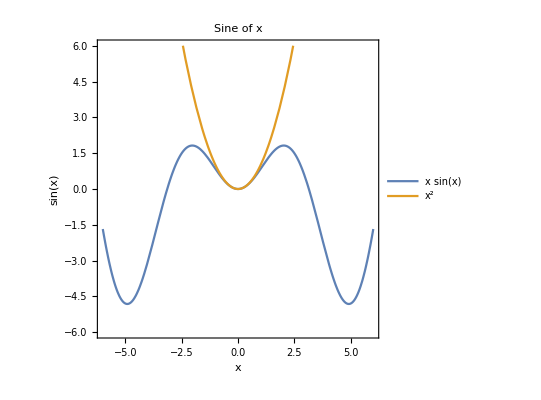

```mathematica
Plot[{x Sin[x],x^2},{x,-6,6},FrameLabel->{x,Sin[x]},PlotLabel->"Sine of x",PlotLegends->"Expressions",PlotRange->{{-6,6}},GridLines->Automatic,AspectRatio->1,Ticks->{Table[{i π,i π},{i,-2,2,1/2}],Automatic},Frame->True](* Comment *)
```

### Oscillations with drag

```mathematica
sol=DSolve[{
x''[t]+k x'[t]+ω^2 x[t]==0,
x[0]==1,
x'[0]==0
},x,t]//First
```

{x→Function[{t},1/(2 √(k^2-4 ω^2))(-ⅇ^(1/2 t (-k-√(k^2-4 ω^2))) k+ⅇ^(1/2 t (-k+√(k^2-4 ω^2))) k+ⅇ^(1/2 t (-k-√(k^2-4 ω^2))) √(k^2-4 ω^2)+ⅇ^(1/2 t (-k+√(k^2-4 ω^2))) √(k^2-4 ω^2))]}

```mathematica
x[1]/.sol/.{k->0.1,ω->1}
```

0.554992+0. ⅈ

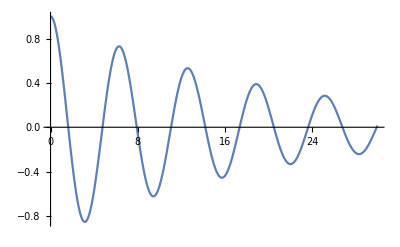

```mathematica
Plot[x[t]/.sol/.{k->0.1,ω->1},{t,0,30}]
```

### Plot3D and Manipulate

```mathematica
Manipulate[
Plot[{x Sin[x],k x^2},{x,-6,6},FrameLabel->{x,Sin[x]},PlotLabel->"Sine of x",PlotLegends->Automatic,PlotRange->{{-6,6}},GridLines->Automatic,AspectRatio->1,Ticks->{Table[{i π,i π},{i,-2,2,1/2}],Automatic},Frame->True],
{k,0.1,1,0.1}
](* Comment *)
```

```mathematica
Plot3D[Sin[x]Cos[y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
data=Table[{x,Gamma[x]},{x,1,4,0.1}]
```

{{1.,1.},{1.1,0.951351},{1.2,0.918169},{1.3,0.897471},{1.4,0.887264},{1.5,0.886227},{1.6,0.893515},{1.7,0.908639},{1.8,0.931384},{1.9,0.961766},{2.,1.},{2.1,1.04649},{2.2,1.1018},{2.3,1.16671},{2.4,1.24217},{2.5,1.32934},{2.6,1.42962},{2.7,1.54469},{2.8,1.67649},{2.9,1.82736},{3.,2.},{3.1,2.19762},{3.2,2.42397},{3.3,2.68344},{3.4,2.98121},{3.5,3.32335},{3.6,3.71702},{3.7,4.17065},{3.8,4.69417},{3.9,5.29933},{4.,6.}}

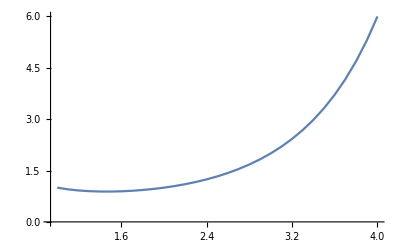

```mathematica
ListPlot[data,Joined->True]
```

```mathematica
data2=Table[{x,y,x+y},{x,1,4,0.1},{y,1,4,0.1}]//Flatten[#,1]&;
```

```mathematica
ListPlot3D[data2]
```

-Graphics3D-

### Miscellaneous♣

Export from cloud

```mathematica
CloudExport[out, "gif", "outX"]
```

Recursive functions

```mathematica
fib[0]=1;
fib[1]=1;
fib[n_Integer/;n>0]:=fib[n-1]+fib[n-2];
Table[fib[n],{n,0,20}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946}

Working with regions

```mathematica
ℛ= HighlightMesh[
DiscretizeGraphics[ExampleData[{"Geometry3D","StanfordBunny"}]],
{Style[1,None],Style[2,Darker@Orange,Opacity[1]]}]
```

-Graphics3D-

```mathematica
NIntegrate[1, x ∈ ℛ]
```

0.0571288

```mathematica
ℒ = Region@CountryData["Latvia", "Polygon"]
```

-Graphics3D-

Working with knowledgebase

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

-Graphics3D-

```mathematica
PhysicalSystemData["HarmonicOscillator1D","DiscreteEnergyEigenvalue"]
```

(1 ℏ) (1/2+n DiscreteQuantumNumber) ω AngularFrequency

```mathematica
(* ctrl+= for wolfram alpha input *)
PhysicalSystemData[LinguisticAssistant, {EntityProperty["PhysicalSystem", 
   "HamiltonianFunction"], 
  EntityProperty["PhysicalSystem", "PotentialEnergy"]}]
```

{-Cos[θ_2 Angle[t Time]] g Acceleration l_2 Length m_2 Mass-Cos[θ_1 Angle[t Time]] g Acceleration l_1 Length (m_1 Mass+m_2 Mass)-((l_2 Length)^2 m_2 Mass (p_(θ,1) AngularMomentum[t Time])^2-2 Cos[θ_1 Angle[t Time]-θ_2 Angle[t Time]] l_1 Length l_2 Length m_2 Mass p_(θ,1) AngularMomentum[t Time] p_(θ,2) AngularMomentum[t Time]+(l_1 Length)^2 (m_1 Mass+m_2 Mass) (p_(θ,2) AngularMomentum[t Time])^2)/((l_1 Length)^2 (l_2 Length)^2 m_2 Mass (-2 m_1 Mass-m_2 Mass+Cos[2 (θ_1 Angle[t Time]-θ_2 Angle[t Time])] m_2 Mass)),-Cos[θ_1 Angle[t Time]] g Acceleration l_1 Length m_1 Mass-g Acceleration (Cos[θ_1 Angle[t Time]] l_1 Length+Cos[θ_2 Angle[t Time]] l_2 Length) m_2 Mass}